```mathematica
Graphics[{Thick,Line[{{{0,0},{6,0}},{{0,0},{0,2}},{{2,0},{2,2}},{{4,0},{4,2}},{{6,0},{6,2}}}],
Text[Style["x_(i + FractionBox[1, 2])",FontSize->16],{4,2.2}],Text[Style["x_(i - FractionBox[1, 2])",FontSize->16],{2,2.2}],Text[Style["x_(i + FractionBox[3, 2])",FontSize->16],{6,2.2}],Text[Style["x_(i - FractionBox[3, 2])",FontSize->16],{0,2.2}],
Text[Style["x_(i - 1)",FontSize->16],{1,.3}],Thick,Line[{{1,0},{1,.1}}],Text[Style["x_i",FontSize->16],{3,.3}],Thick,Line[{{3,0},{3,.1}}],Text[Style["x_(i + 1)",FontSize->16],{5,.3}],Thick,Line[{{5,0},{5,.1}}],
BSplineCurve[{{0,0.9},{1,0},{2,1.7}}],Text[Style["U_(i - 1)",FontSize->16],{1,1}],BSplineCurve[{{2,1},{2.66,2},{3.33,1},{4,1.5}}],Text[Style["U_i",FontSize->16],{3,1.65}],BSplineCurve[{{4,1},{4.66,0},{5.33,2},{6,1.5}}],Text[Style["U_(i + 1)",FontSize->16],{5,1.5}]}]
```

-Graphics-

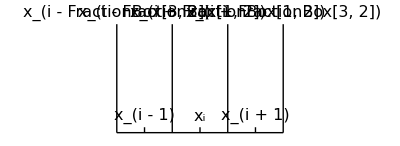

```mathematica
Graphics[{Thick,Line[{{{0,0},{6,0}},{{0,0},{0,2}},{{2,0},{2,2}},{{4,0},{4,2}},{{6,0},{6,2}}}],
Text[Style["x_(i + FractionBox[1, 2])",FontSize->16],{4,2.2}],Text[Style["x_(i - FractionBox[1, 2])",FontSize->16],{2,2.2}],Text[Style["x_(i + FractionBox[3, 2])",FontSize->16],{6,2.2}],Text[Style["x_(i - FractionBox[3, 2])",FontSize->16],{0,2.2}],
Text[Style["x_(i - 1)",FontSize->16],{1,.3}],Thick,Line[{{1,0},{1,.1}}],Text[Style["x_i",FontSize->16],{3,.3}],Thick,Line[{{3,0},{3,.1}}],Text[Style["x_(i + 1)",FontSize->16],{5,.3}],Thick,Line[{{5,0},{5,.1}}]}]
```

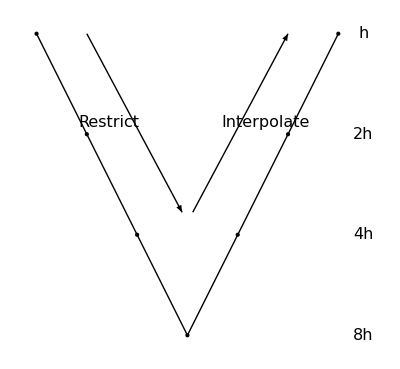

```mathematica
Graphics[{Thick,Line[{{9,6},{12,0},{15,6}}],PointSize[Large],Point[{{9,6},{10,4},{11,2},{12,0},{13,2},{14,4},{15,6}}],
Text[Style["h",FontSize->16],{15.5,6}],
Text[Style["2h",FontSize->16],{15.5,4}],
Text[Style["4h",FontSize->16],{15.5,2}],
Text[Style["8h",FontSize->16],{15.5,0}],
Arrow[{{10,6},{11+2/(√5),2+1/(√5)}}],
Text[Style["Restrict",FontSize->16],{10+1/(√5),4+1/(2 √5)},{0,0},{1,-2}],
Arrow[{{13-2/(√5),2+1/(√5)},{14,6}}],
Text[Style["Interpolate",FontSize->16],{14-1/(√5),4+1/(2 √5)},{0,0},{1,2}]
}]
```

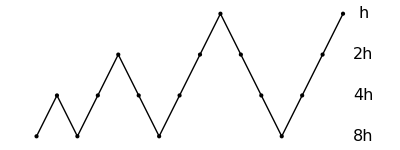

```mathematica
Graphics[{Thick,Line[{{0,0},{1,2},{2,0},{3,2},{4,4},{6,0},{9,6},{12,0},{15,6}}],PointSize[Large],Point[{{0,0},{1,2},{2,0},{3,2},{4,4},{5,2},{6,0},{7,2},{8,4},{9,6},{10,4},{11,2},{12,0},{13,2},{14,4},{15,6}}],
Text[Style["h",FontSize->16],{16,6}],
Text[Style["2h",FontSize->16],{16,4}],
Text[Style["4h",FontSize->16],{16,2}],
Text[Style["8h",FontSize->16],{16,0}]
}]
```

```mathematica
Graphics[{Thick,Line[{{{2,0},{6,0}},{{2,0},{2,2}},{{4,0},{4,2}},{{6,0},{6,2}}}],
Text[Style["x_(i + FractionBox[1, 2])",FontSize->16],{4,2.2}],Text[Style["x_(i - FractionBox[1, 2])",FontSize->16],{2,2.2}],Text[Style["x_(i + FractionBox[3, 2])",FontSize->16],{6,2.2}],
Text[Style["x_i",FontSize->16],{3,.3}],Thick,Line[{{3,0},{3,.1}}],Text[Style["x_(i + 1)",FontSize->16],{5,.3}],Thick,Line[{{5,0},{5,.1}}],
BSplineCurve[{{2,1.1},{4,1.5}}],Text[Style["U_i",FontSize->16],{3,1.5}],BSplineCurve[{{4,1.6},{6,1}}],Text[Style["U_(i + 1)",FontSize->16],{5,1.5}],
Arrow[{{6.5,1},{7.5,1}}],
Text[Style["Restriction",FontSize->16],{7,1.3}],
Thick,Line[{{{8,0},{12,0}},{{8,0},{8,2}},{{12,0},{12,2}}}],
Text[Style["x_(i - FractionBox[1, 2])",FontSize->16],{8,2.2}],Text[Style["x_(i + FractionBox[1, 2])",FontSize->16],{12,2.2}],
Text[Style["x_i",FontSize->16],{10,.3}],
Thick, Line[{{10,0},{10,.1}}],
Line[{{8,1.4},{12,1.2}}],
Text[Style["U_i",FontSize->16],{10,1.5}]},ImageSize->Large]
```

-Graphics-

```mathematica
Graphics[{Thick,Line[{{{0,0},{4,0}},{{0,0},{0,2}},{{4,0},{4,2}}}],
Text[Style["x_(i - FractionBox[1, 2])",FontSize->16],{0,2.2}],Text[Style["x_(i + FractionBox[1, 2])",FontSize->16],{4,2.2}],
Text[Style["x_i",FontSize->16],{2,.3}],
Thick, Line[{{2,0},{2,.1}}],
BSplineCurve[{{0,1},{1,2},{3,0},{4,1.6}}],
Text[Style["U_i",FontSize->16],{2,1.3}],Thick,,
Arrow[{{4.5,1},{5.5,1}}],
Text[Style["Interpolation",FontSize->16],{5,1.3}],Line[{{{6,0},{10,0}},{{6,0},{6,2}},{{8,0},{8,2}},{{10,0},{10,2}}}],
Text[Style["x_(i + FractionBox[1, 2])",FontSize->16],{8,2.2}],Text[Style["x_(i - FractionBox[1, 2])",FontSize->16],{6,2.2}],Text[Style["x_(i + FractionBox[3, 2])",FontSize->16],{10,2.2}],
Text[Style["x_i",FontSize->16],{7,.3}],Thick,Line[{{9,0},{9,.1}}],Text[Style["x_(i + 1)",FontSize->16],{9,.3}],Thick,Line[{{7,0},{7,.1}}],
BSplineCurve[{{6,1},{7,2},{9,0},{10,1.6}}],
Text[Style["U_i",FontSize->16],{7,1.5}],Text[Style["U_(i + 1)",FontSize->16],{9,1.3}]},ImageSize->Large]
```

-Graphics-

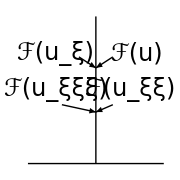

```mathematica
Graphics[{Thick,Line[{{{1,0},{3,0}},{{2,0},{2,2}}}],
Text[Style["ℱ(u)",FontSize->24],{2.6,1.5}],
Arrow[{{2.25,1.45},{2,1.3}}],
Text[Style["ℱ(u_ξ)",FontSize->24],{1.4,1.5}],
Arrow[{{1.75,1.45},{2,1.3}}],
Text[Style["ℱ(u_ξξ)",FontSize->24],{2.5,1}],
Arrow[{{2.25,.8},{2,.7}}],
Text[Style["ℱ(u_ξξξ)",FontSize->24],{1.4,1}],
Arrow[{{1.5,.8},{2,.7}}]
},ImageSize->Small]
```